# Mixed Chinese Postman

Peter Burbery

I analy

## Definition

The mixed chinese postman problem is an arc routing algorithm where the goal is to find the shortest path that crosses each edge and arc at least once in a weighted mixed graph with minimal weight. I developed a paclet for creating random weighted mixed graphs for testing purposes.

Create a random weighted mixed graph with 20 nodes, 54 edges that is 0.68 directed with random integer weights between 1 and 7:

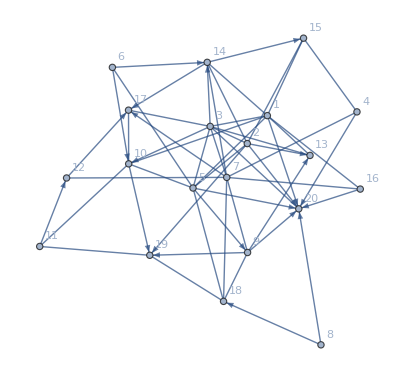

```mathematica
{{-Graphics-, RandomWeightedMixedGraph}}[{20, 54}, 0.68, RandomInteger[{1,7}]&,VertexLabels->Automatic]
```

Mathematica has a function that works for weighted graphs and mixed graphs but not  weighted mixed graphs:

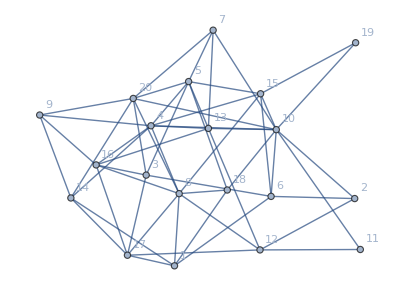
<|-Graphics-→{{1<->18,18<->10,10<->20,20<->14,14<->17,17<->16,16<->13,13<->12,12<->17,17<->8,8<->20,20<->10,10<->19,19<->15,15<->10,10<->13,13<->7,7<->20,20<->9,9<->16,16<->8,8<->18,18<->5,5<->13,13<->5,5<->20,20<->3,3<->17,17<->14,14<->4,4<->13,13<->12,12<->11,11<->10,10<->7,7<->5,5<->15,15<->6,6<->10,10<->4,4<->16,16<->3,3<->17,17<->1,1<->14,14<->9,9<->4,4<->15,15<->8,8<->12,12<->2,2<->10,10<->2,2<->6,6<->3,3<->5,5<->4,4<->8,8<->1,1<->6,6<->1}}|>

```mathematica
AssociationMap[FindPostmanTour,{{{-Graphics-, RandomWeightedMixedGraph}}[{20, 54}, 0, RandomInteger[{1,7}]&,VertexLabels->Automatic]  }]
```

```mathematica
GraphQ[{{-Graphics-, RandomWeightedMixedGraph}}[{20, 54}, 0.68, RandomInteger[{1,7}]&,VertexLabels->Automatic] ]
```

False

FindPostmanTour::ngen: The generalized FindPostmanTour[Graph[<20>, <54>]] is not implemented.

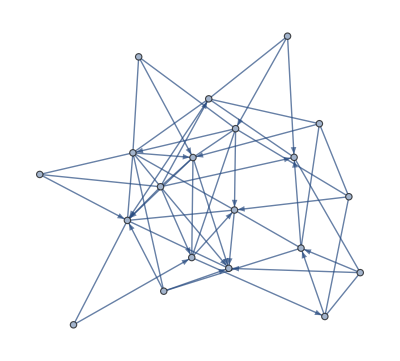
FindPostmanTour[-Graphics-]

```mathematica
FindPostmanTour@{{-Graphics-, RandomWeightedMixedGraph}}[{20,54},0.68,RandomInteger[{1,7}]&]
```